# Vaje iz Mathematice, 1. del

### 1. naloga:

Izračunaj vrednost izraza  ((20+316)^7-55)/(33·12)^3

Izračunaj še numerično vrednost istega izraza na 20 mest natančno.

```mathematica
((20+316)^7-55)/(33*12)^3
```

483476023799709641/62099136

```mathematica
N[((20+316)^7-55)/(33*12)^3, 20]
```

7.7855515381036805568×10^9

### 2. naloga:

Poenostavi izraz  2^x+5a 2^x+2^(x+2)

```mathematica
2^x+5a2^x+2^(x+2) // Simplify
```

5 (2^x+a2^x)

### 3. naloga:

Poišči največji skupni delitelj števil 536, 1248, 2320.

Poišči še najmanjši skupni večkrat teh števil.

```mathematica
GCD[536, 1248, 2320]
```

8

```mathematica
LCM[536, 1248, 2320]
```

12124320

### 4. naloga:

Seštej vsa soda števila na intervalu [1,100].

```mathematica
ClearAll[x]
```

```mathematica
Sum[i, {i ,1000}]
```

500500

### 5. naloga:

Izračunaj  ∑_(k=1)^∞ (k^2+1)/k^4

```mathematica
Sum[(k.b2+1)^2/k^4,{k,∞}]
```

1/90 (1+k.b2)^2 π^4

```mathematica
∑_(k=1)^∞ (k^2+1)/k^4
```

1/90 π^2 (15+π^2)

### 6. naloga:

Izračunaj vrednost izraza (sin α + sin β)/(cos^2(α - β) - sin^2(β-α)) za kota α=1830°  in  β=270°.

```mathematica
α=1830°
β=270°
(Sin[α]+Sin[β])/(Cos[α-β]^2-Sin[β-α]^2)
```

1830 °

270 °

1

### 7. naloga:

Izračunaj vrednost izraza  (x^5-2 x^2+3x+4)/(x^5-2x-1)  pri x=1, 2, ..., 10. 
Uporabi transformacijsko pravilo in ukaz  ReplaceAll  oz.  /.

```mathematica
ClearAll[ans7]
ans7 :=(x^5 - 2*x^2 + 3*x + 4)/(x^5 - 2*x - 1) 
ans7 /. x -> Range[1, 10]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

```mathematica
ans7 /. x -> Table[i,{i,10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

### 8. naloga:

Dan je pravilen šestkotnik s stranico r. Kolikšna je ploščina kolobarja, ki ga določata včrtana in očrtana krožnica?

```mathematica
S = π(r^2 - 3r^2/4)
```

(π r^2)/4

### 9. naloga:

Sin je 3 leta starejši od hčere, mati pa je 23 let starejša od sina. Pred 6 leti je imela mati 4 krat toliko let kot sin in hči skupaj. Koliko je star vsak od njih?

```mathematica
Solve[{s-h==3, m-s == 23, (m-6)==4(s-6+h-6)}]
```

{{h→8,m→34,s→11}}

### 10. naloga:

Poišči vsa kompleksna števila, ki zadoščajo enačbi  z̄=z^2

```mathematica
Reduce[z* ==  z^2]
```

z==0||z==1||z==-1/2-(ⅈ √3)/2||z==-1/2+(ⅈ √3)/2

### 11. naloga:

Koliko začetnih členov zaporedja s splošnim členom  a_n=16-2n  moramo sešteti, da bo vsota enaka 36?

```mathematica
Solve[Sum[16-2n,{n,m}]== 36, m]
```

{{m→3},{m→12}}

### 12. naloga:

Dokaži, da je x=1 rešitev enačbe  a x^2-2b x+c=0, če a, b in c sestavljajo aritmetično zaporedje.

```mathematica
ClearAll[a,b,c, d,x]
```

```mathematica
a*x^2 - 2*b*x + c /. {x-> 1, a-> b +d ,c -> b-d}
```

0

### 13. naloga:

Določi vrednost parametra a v enačbi (2a x+3a)/(3a + 5x)=(3a-4)/(3a + 5x), da bo  x=2  rešitev enačbe.

```mathematica
Solve[(2*a*x + 3*a)/(3*a + 5*x) == (3*a - 4)/(3*a + 5*x) /. x-> 2, a]
```

{{a→-1}}

### 14. naloga:

Na kakšne načine lahko plačamo poštnino 2,27 EUR z znamkami za 10, 23 in 37 centov?

```mathematica
ClearAll[a,b,c]
Length[Solve[{227 == a*10+b*23+c*37, a≥ 0 , b ≥0 , c ≥ 0}, Integers]]
```

5

### 15. naloga:

Poišči štirimestno število, ki je popoln kvadrat in katerega prvi dve števki sta med seboj enaki, drugi dve pa prav tako med seboj enaki.

```mathematica
ClearAll[a,b,c,d]
Solve[{x == n^2, x==1000*a+100*a+10*d+d, a< 10, d < 10},x,PositiveIntegers]
```

{{x→ConditionalExpression[7744,a==7&&d==4&&n==88]}}

### 16. naloga:

Na kocko s stranico a postavimo drugo kocko s telesno diagonalo, enako stranici prve kocke, na drugo kocko spet tretjo s telesno diagonalo, enako stranici druge kocke, in to ponavljamo brez konca. Izračunaj višino tako dobljenega telesa.

Izračunaj še prostornino tako dobljenega telesa.

```mathematica
visina = a/(1-1/√3)
```

a/(1-1/(√3))

```mathematica
Volumen = Sum[(a/(√3)^n)^(3), {n,0, ∞}]
```

-(9 a^3)/(-9+√3)

### 17. naloga:

Določi premico y=k x+n, ki gre skozi točki (-2,3) in (6,-1).

Nariši dobljeno premico na intervalu [-3,7] tako, da bosta enoti na koordinatnih oseh enako veliki.
Na sliki označi še točki, skozi kateri poteka premica.

```mathematica
sol =Solve[3 ==  -2k+ n && -1 == 6k+n, Reals]
```

{{-1/2→-1/2,2→2}}

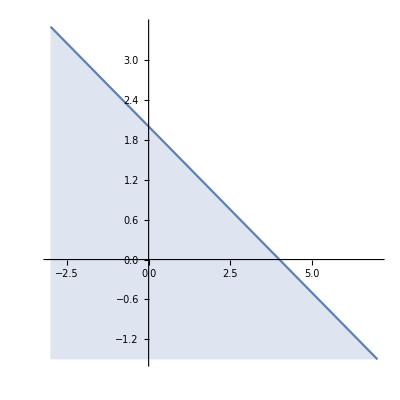

List

```mathematica
{{k->-1/2,n->2}}
k := -1/2
n := 2
Plot[ k*x+n, {x, -3, 7},Filling->Bottom,AspectRatio->1/1]
```

### 18. naloga:

Določi inverzno funkcijo funkcije  y=2ln(3x-1)

Nariši grafa obeh funkcij v istem koordinatnem sistemu.

```mathematica
ClearAll[ff]
ClearAll[y]
ClearAll[x]
ff[x_] := 2*Ln[3*x -1]
ffinverse := Solve[ff[x] ==y /.  {x -> y, y -> x}, y , Reals] // First
ffinverse
g[x_] = y  /.finverse
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

2 Ln[-1+3 y]==x

Solve::nsmet: This system cannot be solved with the methods available to Solve.

ReplaceAll::reps: {2 Ln[-1+3 y]==x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

y/.2 Ln[-1+3 y]==x